# 3R Free Throw Gerik Zatorski

```mathematica
Quit[];
(* TODO:
* Is 0 optimized or should I change it to 0.?
*)
```

## Kinematics of Shot

(Cos[θ0[t]] | -Sin[θ0[t]] | 2
Sin[θ0[t]] | Cos[θ0[t]] | 0
0 | 0 | 1)

ListInterpolation::inhr: Requested order is too high; order has been reduced to {1}.

2+0.25 Cos[                           5
InterpolatingFunction[{{0, -}}, <>]
                           8[t]]+0.121285 Sin[                           5
InterpolatingFunction[{{0, -}}, <>]
                           8[t]]

-0.121285 Cos[                           5
InterpolatingFunction[{{0, -}}, <>]
                           8[t]]+0.25 Sin[                           5
InterpolatingFunction[{{0, -}}, <>]
                           8[t]]

-4.50295

-0.0996962

1.24724

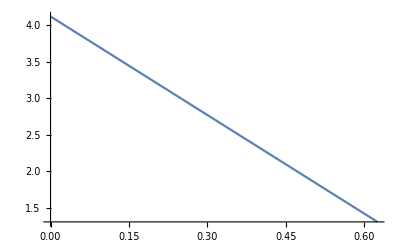

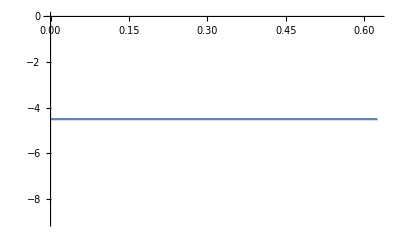

```mathematica
ClearAll["Global`*"]

(* SE(2) representation of rigid body motion in the plane *)
g[x_,y_,θ_]={{Cos[θ],-Sin[θ],x},{Sin[θ],Cos[θ],y},{0,0,1}};
(* unhat takes a 3x3 matrix that is assumed to be ginv.gdot for SE(2) and returns a 3x1 vector. The first two components are the linear velocities in x and y and the third component is the angular velocity (around the "z" axis that is out of the plane of motion *)
unhat[a_]:={a[[1,3]],a[[2,3]],a[[2,1]]};
(* hat[] takes a 3x1 vector and creates a 3x3 matrix *)
hat[a_]:={{0,-a[[3]],a[[1]]},{a[[3]],0,a[[2]]},{0,0,0}};
(* Hom[] takes a point in the plane and adds a 1 to the end of it to create a homogeneous representation of that point. This is used for animation *)
Hom[pt_]:=Flatten[{pt,1}];
(* UnHom[] takes a homogeneous representation of a point and returns the point in the plane by removing the 1 at the end *)
UnHom[pt_]:={pt[[1]],pt[[2]]};
(* Distance between two points in 2D plane *)
Distance2D[x_,y_]:=Sqrt[(x[[1]]-y[[1]])^2+(x[[2]]-y[[2]])^2];

(* Helpers *)
headlist={Or,And,Equal,Unequal,Less,LessEqual,Greater,GreaterEqual,Inequality};
getAllVariables[f_?NumericQ]:=Sequence[]
getAllVariables[{}]:=Sequence[]
getAllVariables[t_]/;MemberQ[headlist,t]:=Sequence[]
getAllVariables[ll_List]:=Flatten[Union[Map[getAllVariables[#]&,ll]]]
getAllVariables[Derivative[n_Integer][f_][arg__]]:=getAllVariables[{arg}]
getAllVariables[f_Symbol[arg__]]:=Module[{fvars},If[MemberQ[Attributes[f],NumericFunction]||MemberQ[headlist,f],fvars=getAllVariables[{arg}],(*else*)fvars=f[arg]];
fvars]
getAllVariables[other_]:=other
extractVariables[formula_]:=With[{pat=_Symbol[___][___]|Subscript[_Symbol,__][___]|Subscript[_Symbol,__]|_Symbol},Union@Cases[formula,pat,-1]]

(* Conversions *)
FtToM=0.3048;

(* Robot Link Lengths Constants *)
(*L1=0.3048*8.5/12;*)
L1=0.3048*60/12;
L1=.5;

(* Ball Constants *)
m=0.625;
diameterBall=9.55/12*FtToM;
rball=diameterBall/2;

(* World to Joint Frame Transformations *)
g0=g[2,0,0].g[0,0,θ0[t]];
%//MatrixForm
ghand=g0.g[L1/2,0,0];
gEE=g0.g[L1,0,0].g[0,0,0];

(* World to Ball Frame Transformations prior to roll*)
gballbefore=g0.g[L1/2,-rball,0];
gline1before=gballbefore.g[-rball,0,0];
gline2before=gballbefore.g[rball,0,0];

(* Joint Velocities *)
θ0sol=ListInterpolation[{Pi*21/16,Pi*5/12},{0,5/8}][t];
(*θ0dotsol=(Pi*5/12-Pi*21/16)/(5/8)*)
θ0dotsol=D[θ0sol,t];

(*********************************** Shot Animation ****************************************)
coordJoint0[t_]:=({g0[[1,3]],g0[[2,3]]})/.t->time;
coordEE[time_]:=({gEE[[1,3]],gEE[[2,3]]}/.{θ0[t]->θ0sol})/.t->time;
coordballbefore[time_]:=({gballbefore[[1,3]],gballbefore[[2,3]]}/.{θ0[t]->θ0sol})/.t->time;
coordline1before[time_]:=({gline1before[[1,3]],gline1before[[2,3]]}/.{θ0[t]->θ0sol})/.t->time;
coordline2before[time_]:=({gline2before[[1,3]],gline2before[[2,3]]}/.{θ0[t]->θ0sol})/.t->time;

(* Joint Graphics *)
GraphicsL1=Line[{coordJoint0[t],coordEE[t]}];

(* Ball Graphics *)
Graphicsballbefore = Circle[coordballbefore[t],rball];
Graphicsballlinebefore=Line[{coordline1before[t],coordline2before[t]}];

(* Solving for conditions at roll *)
troll=0.1;
tr=gballbefore/.{θ0[t]->θ0sol};
xr=tr[[1,3]]/.t->troll;
yr=tr[[2,3]]/.t->troll;

tr[[1,3]]
tr[[2,3]]

(*θr=N[ArcCos[tr[[1,1]]]];*)
θr=((θ0[t]))/.{θ0[t]->θ0sol}/.t->troll;

(* dot sol estimation *)
(*tr1=gballbefore/.{θ0[t]->θ0sol}/.t->(troll-.01);
tr2=gballbefore/.{θ0[t]->θ0sol}/.t->(troll+.01);
θrdot=N[(ArcCos[tr2[[1,1]]]-ArcCos[tr1[[1,1]]])/.02]
xrdot=N[(tr2[[1,3]]-tr1[[1,3]])/.02]
yrdot=N[(tr2[[2,3]]-tr1[[2,3]])/.02]*)
(*θrdot=N[(ArcCos[tr2[[1,1]]]-ArcCos[tr[[1,1]]])/.01]
xrdot=N[(tr2[[1,3]]-tr[[1,3]])/.01]
yrdot=N[(tr2[[2,3]]-tr[[2,3]])/.01]*)

(* dot sol exact *)
θrdot=θ0dotsol/.t->troll
trdot=D[gballbefore,t]/.{θ0[t]->θ0sol,θ0'[t]->θ0dotsol};
(*trdot=D[gballbefore,t];*)
xrdot=trdot[[1,3]]/.t->troll
yrdot=trdot[[2,3]]/.t->troll

Plot[θ0sol,{t,0,5/8}]
Plot[θ0dotsol,{t,0,5/8}]

(* Animations *)
Animate[
Show[
Graphics[{
Black,GraphicsL1/.t->time,
Black,Graphicsballbefore/.t->time,
Black,Graphicsballlinebefore/.t->time
},
(*PlotRange->{{-1,8},{-1,8}},*)Axes->True]
],
{time,0,5/8},
AnimationRunning->False,
AnimationRate->1.0
]
```

## roll constraint and roll off “fingertips”

{Cos[θ0[t]],Sin[θ0[t]],θ[t],θ0[t],θ'[t],θ0'[t],θ''[t],θ0''[t]}

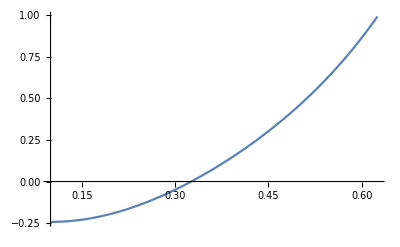

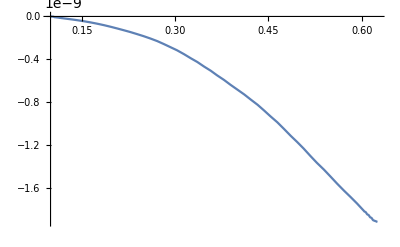

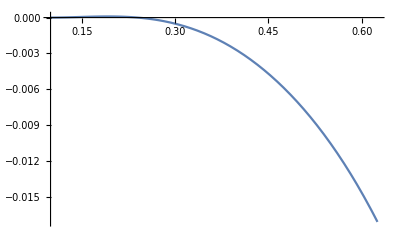

-Graphics-

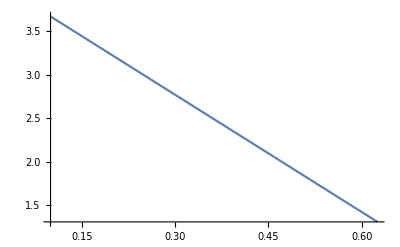

```mathematica
(* Configuration Variables *)
q={{x[t],y[t],θ[t]}}ᵀ;
dq=D[q,t];
ddq=D[dq,t];

(* New Ball Frame Transforms for time after roll *)
gball=g[x[t],y[t],0].g[0,0,θ[t]];
gline1=gball.g[-rball,0,0];
gline2=gball.g[rball,0,0];
ghandball=Inverse[ghand].gball; (* ball in hand frame *)
(*θhandball=ArcCos[ghandball[[1,1]]];*)
θhandball=θ[t]-θ0[t];
xhandball=ghandball[[1,3]];
gcontact=g0.g[L1/2-rball*θhandball,0,0];
contacta=D[D[gcontact,t],t];
Variables@%

gcontactx=(gcontact[[1,3]])/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol};
gcontacty=(gcontact[[2,3]])/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol};
coordcontact[time_]:={First[gcontactx],First[gcontacty]}/.t->time;
Graphicscontact=Locator[{First[gcontactx],First[gcontacty]}];

(* Lagrangian using body velocities (see lecture 23) *)
Vball=unhat[Inverse[gball].D[gball,t]];
Iball=DiagonalMatrix[{m,m,J}];
J=1;
KE=1/2*(Vball.Iball).{Vball}ᵀ;
PE=m*grav*y[t];
Lag =KE-PE;

(* External forces *)
Fhandx=m*contacta[[1,3]]/.{θ0[t]->θ0sol,θ0'[t]->θ0dotsol,θ0''[t]->0};
Fhandy=m*contacta[[2,3]]/.{θ0[t]->θ0sol,θ0'[t]->θ0dotsol,θ0''[t]->0};

(* Constraints *)
(* Ball remains in contact with last link *)
ϕa=ghandball[[2,3]]-rball;

(* Ball rolls without slipping where x=rball*θ *)
ϕb=xhandball-rball*θhandball;
(*Variables@%
D[ϕb,t];
Variables@%
D[D[ϕb,t],t]
Variables@%*)


(* Ball rolls without slipping where v=rball*ω *)
(*Variables@%*)

(* gotta do this *)
θ0[t]=θ0sol;
(*θ0'[t]=θ0dotsol;
θ0''[t]=0;*)

(* Euler-Lagrange equations VECTORS *)
(*Eq1=D[D[Lag,x'[t]],t]-D[Lag,x[t]]==0;
Eq2=D[D[Lag,y'[t]],t]-D[Lag,y[t]]==0;
Eq3=D[D[Lag,θ'[t]],t]-D[Lag,θ[t]]==0;*)

(*Eq1=D[D[Lag,x'[t]],t]-D[Lag,x[t]]==λa*D[ϕa,x[t]]+λb*D[ϕb,x[t]];
Eq2=D[D[Lag,y'[t]],t]-D[Lag,y[t]]==λa*D[ϕa,y[t]]+λb*D[ϕb,y[t]];
Eq3=D[D[Lag,θ'[t]],t]-D[Lag,θ[t]]==λa*D[ϕa,θ[t]]+λb*D[ϕb,θ[t]];
Eq4=D[D[ϕa,t],t]==0;*)

(* a constraint *)
(*Eq1=D[D[Lag,x'[t]],t]-D[Lag,x[t]]==λa*D[ϕa,x[t]];
Eq2=D[D[Lag,y'[t]],t]-D[Lag,y[t]]==λa*D[ϕa,y[t]];
Eq3=D[D[Lag,θ'[t]],t]-D[Lag,θ[t]]==λa*D[ϕa,θ[t]];
Eq4=D[D[ϕa,t],t]==0;*)

(* b constraint *)
Eq1=D[D[Lag,x'[t]],t]-D[Lag,x[t]]==λb*D[ϕb,x[t]]+Fhandx;
Eq2=D[D[Lag,y'[t]],t]-D[Lag,y[t]]==λb*D[ϕb,y[t]]-Fhandy;
Eq3=D[D[Lag,θ'[t]],t]-D[Lag,θ[t]]==λb*D[ϕb,θ[t]];
Eq4=D[D[ϕb,t],t]==0;

(* BOTH constraints *)
(*Eq1=D[D[Lag,x'[t]],t]-D[Lag,x[t]]==λa*D[ϕa,x[t]]+λb*D[ϕb,x[t]];
Eq2=D[D[Lag,y'[t]],t]-D[Lag,y[t]]==λa*D[ϕa,y[t]]+λb*D[ϕb,y[t]];
Eq3=D[D[Lag,θ'[t]],t]-D[Lag,θ[t]]==λa*D[ϕa,θ[t]]+λb*D[ϕb,θ[t]];
Eq4=D[D[ϕa,t],t]==0;
Eq5=D[D[ϕb,t],t]==0;*)

(*ELtemp=Solve[{Eq1&&Eq2&&Eq3},{x''[t],y''[t],θ''[t]}];*)
ELtemp=Solve[{Eq1&&Eq2&&Eq3&&Eq4},{x''[t],y''[t],θ''[t],λb}];
(*ELtemp=Solve[{Eq1&&Eq2&&Eq3&&Eq4&&Eq5},{x''[t],y''[t],θ''[t],λa,λb}];*)
EL={x''[t]==ELtemp[[1,1,2]],y''[t]==ELtemp[[1,2,2]],θ''[t]==ELtemp[[1,3,2]]};

(* Constants *)
grav = 9.8;

(* Initial Condition *)
InitCon={x[troll]==xr,y[troll]==yr,θ[troll]==θr,x'[troll]==xrdot,y'[troll]==yrdot,θ'[troll]==θrdot};

(* Numerical Solution *)
tmax =5/8;
sol=NDSolve[Join[EL,InitCon],{x,y,θ},{t,troll,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4}];
(*sol=NDSolve[Join[EL,InitCon],{x,y,θ},{t,troll,tmax}];*)

xsol=x[t]/.sol;
ysol=y[t]/.sol;
θsol=θ[t]/.sol;

(* plots *)
(*Plot[(xhandball)/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tmax}]
Plot[ghandball[[2,3]]/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tmax}]
Plot[θhandball/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tmax}]
Plot[(gcontact[[1,3]])/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tmax}]*)

(* plot constraints *)
Plot[ϕa/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tmax}]
Plot[ϕb/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tmax}]

Plot[(xhandball)/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tmax}]
Plot[(rball*θhandball)/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tmax}]
Plot[θ0[t]/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tmax}]


(* Dynamic ball coords and graphics *)
coordball[time_]:=({gball[[1,3]],gball[[2,3]]}/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
coordline1[time_]:=({gline1[[1,3]],gline1[[2,3]]}/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
coordline2[time_]:=({gline2[[1,3]],gline2[[2,3]]}/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
Graphicsball = Circle[{coordball[t][[1]][[1]],coordball[t][[2]][[1]]},rball];
Graphicsballline=Line[{{coordline1[t][[1]][[1]],coordline1[t][[2]][[1]]},{coordline2[t][[1]][[1]],coordline2[t][[2]][[1]]}}];

Animate[
Show[
Graphics[{
Black,GraphicsL1/.t->time,
Black,Graphicsball/.t->time,
Black,Graphicsballline/.t->time,
Graphicscontact/.t->time
}],
(*PlotRange->{{-1,8},{-1,8}},*)
Axes->True
],
{time,troll,tmax},
AnimationRunning->False,
AnimationRate->1.0
]
```

## Shot Result

```mathematica
(* Configuration Variables *)
q={{x[t],y[t],θ[t]}}ᵀ;
dq=D[q,t];
ddq=D[dq,t];

(* Lagrangian *)
Iball=2/3*m*rball^2;
KE=1/2*m*(x'[t]^2+y'[t]^2)+1/2*Iball*θ'[t]^2;
PE=m*g*y[t];
L=KE-PE;

(* Euler-Lagrange equations *)
Eq=(Thread[D[L,qᵀ]-D[D[L,dqᵀ],t]==0]);
ELtemp=Solve[Eq[[1]]&&Eq[[2]]&&Eq[[3]],{y''[t],x''[t],θ''[t]}];
EL={y''[t]==ELtemp[[1,1,2]],x''[t]==ELtemp[[1,2,2]],θ''[t]==ELtemp[[1,3,2]]};

(* Hamiltonian *)
p=D[L,dqᵀ];
H=p.dq-L;

(* Impact Equations - solving for velocities after impact *)
(* Impact with ground *)
ϕ0=y[t]-rball;
ChangeMomentum=Thread[(D[L,dqᵀ]/.(x'[t]->ϕ0dq1p)/.(y'[t]->ϕ0dq2p)/.(θ'[t]->ϕ0dq3p))-(D[L,dqᵀ])==λ*D[ϕ0,qᵀ]];
Hn = H;
Hp = H/.(x'[t]->ϕ0dq1p)/.(y'[t]->ϕ0dq2p)/.(θ'[t]->ϕ0dq3p);
ConserveH=(Hp==Hn);
IEq=Solve[ChangeMomentum[[1]]&&ChangeMomentum[[2]]&&ChangeMomentum[[3]]&&ConserveH,{ϕ0dq1p,ϕ0dq2p,ϕ0dq3p,λ}];
ϕ0dq1p=IEq[[1,1,2]]*c;
ϕ0dq2p=IEq[[1,2,2]]*c;
ϕ0dq3p=IEq[[1,3,2]];
(* Impact with backboard *)
ϕ1=x[t]+rball+BaselineToBackboard;
ChangeMomentum=Thread[(D[L,dqᵀ]/.(x'[t]->ϕ1dq1p)/.(y'[t]->ϕ1dq2p)/.(θ'[t]->ϕ1dq3p))-(D[L,dqᵀ])==λ*D[ϕ1,qᵀ]];
Hn = H;
Hp = H/.(x'[t]->ϕ1dq1p)/.(y'[t]->ϕ1dq2p)/.(θ'[t]->ϕ1dq3p);
ConserveH=(Hp==Hn);
IEq=Solve[ChangeMomentum[[1]]&&ChangeMomentum[[2]]&&ChangeMomentum[[3]]&&ConserveH,{ϕ1dq1p,ϕ1dq2p,ϕ1dq3p,λ}];
ϕ1dq1p=IEq[[1,1,2]]*c;
ϕ1dq2p=IEq[[1,2,2]]*c;
ϕ1dq3p=IEq[[1,3,2]];
(* Impact with front rim *)
ϕ2=Distance2D[{x[t],y[t]},{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2}]-RimThickness/2-rball;
ChangeMomentum=Thread[(D[L,dqᵀ]/.(x'[t]->ϕ2dq1p)/.(y'[t]->ϕ2dq2p)/.(θ'[t]->ϕ2dq3p))-(D[L,dqᵀ])==λ*D[ϕ2,qᵀ]];
Hn = H;
Hp = H/.(x'[t]->ϕ2dq1p)/.(y'[t]->ϕ2dq2p)/.(θ'[t]->ϕ2dq3p);
ConserveH=(Hp==Hn);
IEq=Solve[ChangeMomentum[[1]]&&ChangeMomentum[[2]]&&ChangeMomentum[[3]]&&ConserveH,{ϕ2dq1p,ϕ2dq2p,ϕ2dq3p,λ}];
ϕ2dq1p=IEq[[2,1,2]]*c;
ϕ2dq2p=IEq[[2,2,2]]*c;
ϕ2dq3p=IEq[[2,3,2]];
(* Impact with back rim *)
ϕ3=Distance2D[{x[t],y[t]},{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2}]-RimThickness/2-rball;
ChangeMomentum=Thread[(D[L,dqᵀ]/.(x'[t]->ϕ3dq1p)/.(y'[t]->ϕ3dq2p)/.(θ'[t]->ϕ3dq3p))-(D[L,dqᵀ])==λ*D[ϕ3,qᵀ]];
Hn = H;
Hp = H/.(x'[t]->ϕ3dq1p)/.(y'[t]->ϕ3dq2p)/.(θ'[t]->ϕ3dq3p);
ConserveH=(Hp==Hn);
IEq=Solve[ChangeMomentum[[1]]&&ChangeMomentum[[2]]&&ChangeMomentum[[3]]&&ConserveH,{ϕ3dq1p,ϕ3dq2p,ϕ3dq3p,λ}];
ϕ3dq1p=IEq[[1,1,2]]*c;
ϕ3dq2p=IEq[[1,2,2]]*c;
ϕ3dq3p=IEq[[1,3,2]];

(* Constants *)
g=9.8;
(* Coefficient of Restitution *)
c=0.8;

(* Initial Conditions - TODO: replace these with results from shot dynamics.08.08*)
(* Impacts with backboard, front rim *)
(*InitCon={x[0]==-BaselineToFoulLine,y[0]==6.5*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};*)
(* Impacts with backboard, back rim *)
(*InitCon={x[0]==-BaselineToFoulLine,y[0]==5.5*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};*)
(* Impacts with backboard, MAYBE front rim back rim *)
InitCon={x[0]==-BaselineToFoulLine,y[0]==5.8*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};
(* Impacts with front rim - short shot *)
(*InitCon={x[0]==-BaselineToFoulLine,y[0]==4.2*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};*)
(* over the backboard *)
(*InitCon={x[0]==-BaselineToFoulLine,y[0]==8.3*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};*)

(* Numerical Solution *)
tmax=5;
newxdot=0;
newydot=0;
newθdot=0;
(* TODO: better options to avoid missing (ex. "back rim" printed when tmax=5, but no change in direction) *)
{sol,{times}}=NDSolve[Join[EL,InitCon,
(* impact with ground *)
{WhenEvent[y[t]-rball==0,{Print["Ground Impact"],end=t,Print[end],newxdot=N[ϕ0dq1p],newydot=N[ϕ0dq2p],newθdot=N[ϕ0dq3p],x'[t]->newxdot,y'[t]->newydot,θ'[t]->newθdot},"DetectionMethod"->"Interpolation"]},
(* impact with backboard - TODO: improve y triggers*)
{WhenEvent[x[t]+rball+BaselineToBackboard==0&&y[t]<(BackboardBaseHeight+GroundToBackboard)&&y[t]>BackboardBaseHeight,{Print["Backboard!"],end=t,Print[end],newxdot=N[ϕ1dq1p],newydot=N[ϕ1dq2p],newθdot=N[ϕ1dq3p],x'[t]->newxdot,y'[t]->newydot,θ'[t]->newθdot},"DetectionMethod"->"Interpolation"]},
(* impact with front rim *)
{WhenEvent[Distance2D[{x[t],y[t]},{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2}]-RimThickness/2-rball==0,{Print["Front Rim Impact!"],end=t,Print[end],newxdot=N[ϕ2dq1p],newydot=N[ϕ2dq2p],newθdot=N[ϕ2dq3p],x'[t]->newxdot,y'[t]->newydot,θ'[t]->newθdot,Print[newxdot],Print[newydot]},
"DetectionMethod"->"Interpolation",
"IntegrateEvent"->True,
"LocationMethod"->{"Brent",AccuracyGoal->12,PrecisionGoal->12}]},
(* impact with back rim *)
{WhenEvent[Distance2D[{x[t],y[t]},{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2}]-RimThickness/2-rball==0,
{Print["Back Rim Impact!"],end=t,Print[end],newxdot=N[ϕ3dq1p],newydot=N[ϕ3dq2p],newθdot=N[ϕ3dq3p],x'[t]->newxdot,y'[t]->newydot,θ'[t]->newθdot,Print[newxdot],Print[newydot]},
"DetectionMethod"->"Interpolation",
"LocationMethod"->{"Brent",AccuracyGoal->12,PrecisionGoal->12}]}
],{x,y,θ},{t,0,tmax}]//Reap;



(*ListPlot[RealExponent[Differences[times]]]*)

xsol=First[x[t]/.sol];
ysol=First[y[t]/.sol];
θsol=First[θ[t]/.sol];

Plot[Distance2D[{xsol,ysol},{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2,0}]-RimThickness/2-rball,{t,0,tmax}]

(* Dynamic Graphics *)
BallGraphic=Circle[{xsol,ysol},diameterBall/2];
BallLineGraphic=Line[{{xsol-rball*Cos[θsol],ysol-rball*Sin[θsol]},{xsol+rball*Cos[θsol],ysol+rball*Sin[θsol]}}];

(* Static Graphics *)
FloorGraphic=Line[{{-22*FtToM,0},{0,0}}];
BackboardGraphic=Line[{{-BaselineToBackboard,BackboardBaseHeight},{-BaselineToBackboard,BackboardBaseHeight+GroundToBackboard}}];
FrontRimGraphic=Disk[{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2},RimThickness/2];
BackRimGraphic=Disk[{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2},RimThickness/2];
NetFrontGraphic=Line[{{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2},{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2-.2}}];
NetBackGraphic=Line[{{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2},{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2-.2}}];
HitchGraphic=Line[{{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2},{-BaselineToBackboard,GroundToRim-RimThickness/2}}];

(*Animate[
Show[
Graphics[{
Black,BallGraphic/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,BackboardGraphic,
Black,BackRimGraphic,
Black,FrontRimGraphic,
GrayLevel[0.86],NetBackGraphic,
GrayLevel[0.86],NetFrontGraphic,
Black,HitchGraphic
}],
PlotRange->{{-8,1},{-1,6}},
Axes->True,
ImageSize->Full
],
{time,0,tmax},
AnimationRunning->False,
AnimationRate->0.4,
ContentSize->{1000,800}
]

Animate[
Show[
Graphics[{
Black,BallGraphic/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,BackboardGraphic,
Black,BackRimGraphic,
Black,FrontRimGraphic,
GrayLevel[0.86],NetBackGraphic,
GrayLevel[0.86],NetFrontGraphic,
Black,HitchGraphic
}],
PlotRange->{{-2.5,-1},{2.5,4.1}},
Axes->True,
ImageSize->Full
],
{time,0,tmax},
AnimationRunning->False,
AnimationRate->0.4,
ContentSize->{800,700}
]

graphics = Graphics[{
Black,BallGraphic/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,BackboardGraphic,
Black,BackRimGraphic,
Black,FrontRimGraphic,
GrayLevel[0.86],NetBackGraphic,
GrayLevel[0.86],NetFrontGraphic,
Black,HitchGraphic
},PlotRange->{{-8,1},{-1,6}},
Axes->True]

frames=Table[graphics,{time,0,tmax,0.1}];
anim=ListAnimate[frames,AnimationRate->0.4];
Export["~/Desktop/Court_View.gif",frames];

graphics = Graphics[{
Black,BallGraphic/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,BackboardGraphic,
Black,BackRimGraphic,
Black,FrontRimGraphic,
GrayLevel[0.86],NetBackGraphic,
GrayLevel[0.86],NetFrontGraphic,
Black,HitchGraphic
},
PlotRange->{{-2.5,-1},{2.5,4.1}},Axes->True]

frames=Table[graphics,{time,0,tmax,0.01}];
anim=ListAnimate[frames,AnimationRate->0.4];
Export["~/Desktop/Basket_View.gif",frames];*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::ndinnt: Initial condition -1. BaselineToFoulLine is not a number or a rectangular array of numbers.

Set::shape: Lists {times} and {} are not the same shape.

ReplaceAll::reps: {NDSolve[{y''[t]==-9.8,x''[t]==0.,«10»,WhenEvent[Distance2D[{«2»},{«2»}]-Times[«2»]-rball==0,{Print[Back Rim Impact!],end=t,Print[end],newxdot=N[ϕ3dq1p],newydot=N[ϕ3dq2p],newθdot=N[ϕ3dq3p],x'[t]→newxdot,y'[t]→newydot,θ'[t]→newθdot,Print[newxdot],Print[newydot]},DetectionMethod→Interpolation,LocationMethod→{Brent,AccuracyGoal→12,PrecisionGoal→12}]},{x,y,θ},{t,0,5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-Graphics-